# 1.labor

## 1.feladat

```mathematica
t1=3^Range[0,20]
```

{1,3,9,27,81,243,729,2187,6561,19683,59049,177147,531441,1594323,4782969,14348907,43046721,129140163,387420489,1162261467,3486784401}

```mathematica
t2=Table[3^(i-1),{i,21}]
```

{1,3,9,27,81,243,729,2187,6561,19683,59049,177147,531441,1594323,4782969,14348907,43046721,129140163,387420489,1162261467,3486784401}

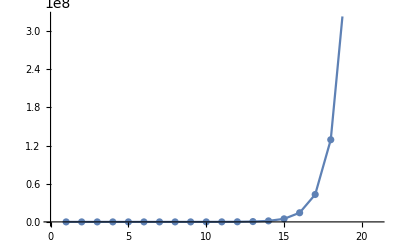

```mathematica
Show[
	ListLinePlot[t2],
	ListPlot[t1]
]
```

## 2. feladat

```mathematica
l1=Line[{{1,0},{2,1}}];
l2=Line[{{1,1},{2,0}}];
Animate[
	  Graphics[
			  Rotate[{l1,l2},alfa],
			  PlotRange->{{0.5,2.5},{-0.5,1.5}}],
	{alfa,0,5},
	AnimationRunning->False
]
```

## 3. feladat

```mathematica
Animate[ 
	Manipulate[ 
		Show[
			ParametricPlot[{x0+v*Cos[szog]*t,y0+v*Sin[szog]*t-5*t^2}, {t, 0, 10}],
			Graphics[  Disk[{x0+v*Cos[szog]*t,y0+v*Sin[szog]*t-5*t^2},5]] ],
		{x0,-10,10},
		{y0,-10,10},
		{szog,0,Pi},
		{v,0,50}],	  
	{t,0,10},
	AnimationRunning->False
]
```

## 4. feladat

```mathematica
f1=DSolveValue[y'[x]==2*x*y[x],y[x],x];
```

```mathematica
ⅇ^(x^2) C[1]
```

```mathematica
Manipulate[
	Plot[c*Exp[x^2],{x,-1,1},PlotRange->{{-10,10},{-10,10}}],
	{c,-5,5}
]
```

## 5. feladat

InterpolatingFunction::dmval: Input value {-1.99992} lies outside the range of data in the interpolating function. Extrapolation will be used.

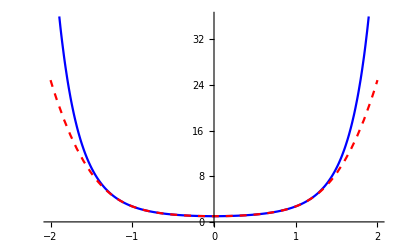

```mathematica
sol=DSolveValue[{y'[x]==2*x*y[x],y[0]==1},y,x];
nsol=NDSolveValue[{y'[x]==2*x*y[x],y[0]==1},y,{x,-1,1}];
Show[
	Plot[sol[x],{x,-2,2},PlotStyle->{Blue}],
	Plot[nsol[x],{x,-2,2},PlotStyle->{Red, Dashed}]
]
```